## Lightning Introduction to Mathematica Notebooks

## January 13, 2025

## Heads or Tails

### Heads or Tails

There are many ways to generate heads or tails at random in Mathematica. Here is a one-liner:

```mathematica
RandomChoice[{"H", "T"}]
```

H

We are going to use this one-liner a lot and it would not be much work to copy and paste it over and over, but it would be nice if we saved a few characters by defining a function:

```mathematica
headsOrTails[]:=RandomChoice[{"H", "T"}]
```

Let’s call the function once:

```mathematica
headsOrTails[]
```

H

Let’s call the function five times:

```mathematica
{headsOrTails[], headsOrTails[],headsOrTails[],headsOrTails[], headsOrTails[]}
```

{H,T,T,T,H}

### Counting Heads — 1 Coin Toss

Let’s do a new version of this function that takes a count of the number of heads that have so far happened as an argument, and adds one to it, but only if the next coin toss is a head:

```mathematica
countHeads[count_]:=If[RandomChoice[{"H", "T"}]=="H", count+1, count]
```

```mathematica
countHeads[0]
```

1

### Counting Heads — 3 Coin Tosses

Here I have nested the function for a total of three calls:

```mathematica
countHeads[countHeads[countHeads[0]]]
```

2

### Counting Heads — 10 Coin Tosses

Here I have nested the function for a total of ten calls, and used white space and indenting to make it clearer what is happening:

```mathematica
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[
countHeads[0]
]
]
]
]
]
]
]
]
]
```

5

### Counting Heads — 100 Coin Tosses

Mathematica has a function that does exactly this kind of nesting, and it is called Nest. Nest takes three arguments: the function, the argument to the innermost function call, and the number of iterations.

```mathematica
Nest[countHeads,0,100]
```

45

### Counting Heads — 100 Coin Tosses — Keeping Intermediate Results

You might want more than just the final result. Very handily, another version of Nest, called NestList, keeps all the intermediate results!

```mathematica
NestList[countHeads,0,100]
```

{0,1,1,2,3,4,4,4,5,5,5,5,5,5,6,7,8,9,9,10,10,11,12,13,14,15,15,15,15,15,16,16,17,18,18,18,19,20,20,20,20,21,22,23,24,25,25,25,26,26,26,27,28,28,28,29,29,30,30,31,31,32,32,33,34,34,35,35,35,36,36,37,37,38,39,40,40,41,41,42,43,43,44,44,45,45,46,46,47,47,47,47,48,48,49,50,51,51,51,51,51}

### Counting Heads — 1000 Coin Tosses — Keeping Intermediate Results — Suppressing Display of All but Last Result

Once we get to 1000 coin tosses, we probably don’t want to see all the intermediate results:

```mathematica
lotsaTosses=NestList[countHeads,0,1000];
```

The semi-colon suppresses the display of the output. Perhaps you still want to see the final total which is the last item in the list:

```mathematica
Last[lotsaTosses]
```

488

### Displaying Heads in 1000 Coin Tosses as a Graph

Displaying all the intermediate results for 1000 coin tosses is well done with a graph:

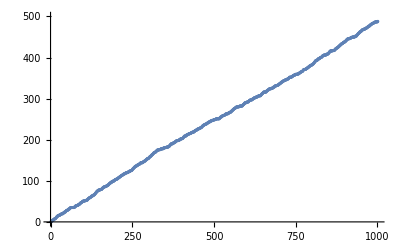

```mathematica
ListPlot[lotsaTosses, PlotRange->{{0,1000},{0,500}}]
```